## Common

```mathematica
Needs["PlotLegends`"]
```

```mathematica
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
```

```mathematica
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
```

This function reads single stat for all experiment runs by multiple parameters/methods. Typical use for "experiments_???.txt" file.

```mathematica
readFinalStats[names_List,statName_]:=
Module[{allData},
allData = ImportString[Import[#],"TSV"]&/@names;
allData⟦#⟦1⟧,2;;,#⟦3⟧⟧&/@Position[allData,statName]
]
```

Reads all stat names from multiple parameters/methods. Returns their intersection.

```mathematica
readFinalStatNames[names_List]:=
Module[{allData},
Flatten[Intersection[(ImportString[Import[#],"TSV"]&/@names)⟦All,1,All⟧]]
]
```

```mathematica
listAllExperimentFiles[dirs_List]:=
Flatten[FileNames[RegularExpression["experiments\\_\\d\\d\\d\\.txt"],{"/Users/drchaj1/java/exp/"<>#}]&/@dirs]
```

## Fitness of a Single Run

```mathematica
{data, bsf, avg, med, min}=readRunFitness["~/java/exp/results/run_001_001_FITNESS.txt"];
```

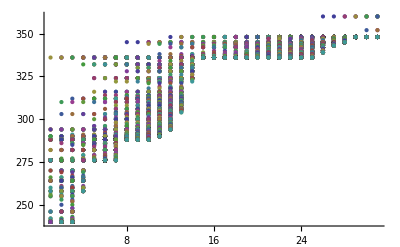

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

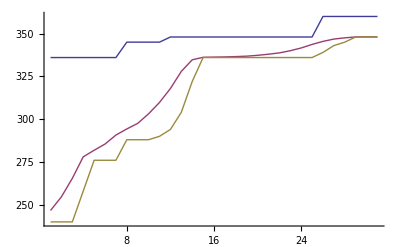

```mathematica
ListLinePlot[{bsf, avg, min}, PlotRange->All]
```

## Fitness over Multiple Runs

```mathematica
bsfAvg = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
enlarge[list_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvg=Mean[(enlarge/@bsfAvg)];
```

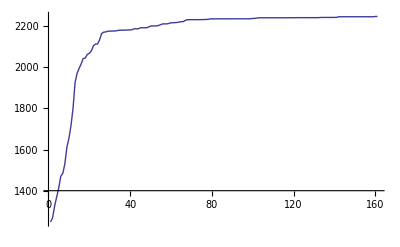

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

## Evaluation of a Single Run

```mathematica
{data, max, avg, med, min}=readRunEvaluationInfo["~/java/exp/results/run_001_001_AVG_DISTANCE.txt"];
```

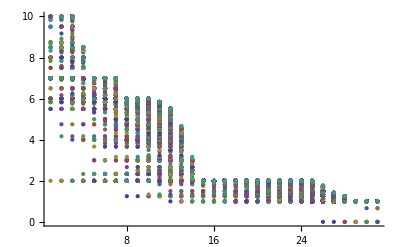

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

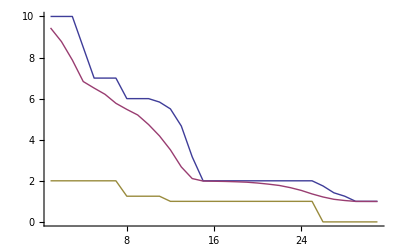

```mathematica
ListLinePlot[{max, avg, min}, PlotRange->All]
```

## Evaluation over Multiple Runs

```mathematica
bsfAvg = (readRunEvaluationInfo[#]⟦5⟧&/@FileNames["run_001*AVG_DISTANCE.txt",{"~/java/exp/results"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

161

```mathematica
bsfAvg=Mean[enlarge[#,Min[bsfAvg], bsfAvg]&/@bsfAvg];
```

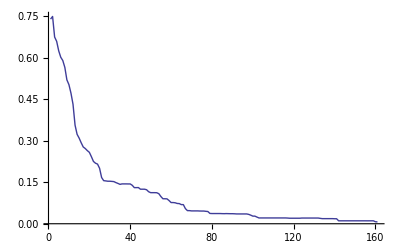

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```

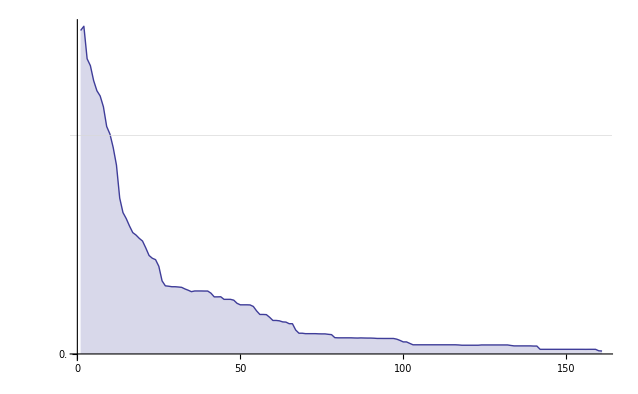

```mathematica
Show[ListLinePlot[{bsfAvg[[1;;]]}, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},Filling->Axis,AxesOrigin->{0,0}], GridLines->{None, {0.5}}]
```

## Evaluation over Multiple Methods

```mathematica
singleMethod[methodDir_, variable_, column_] :=
Module[{stat},
stat=(readRunFitness[#]⟦column⟧&/@(Complement[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]));
Mean[enlarge[#,Max[#], stat]&/@stat]
]
```

```mathematica
singleMethodGeneralization[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
Intersection[FileNames["run_001*"<>variable<>".txt",{"~/java/exp/results/"<>methodDir}],FileNames["run_001*GENERALIZATION*.txt",{"~/java/exp/results/"<>methodDir}]]);
Mean[enlarge[#,Min[#], stat]&/@stat]
]
```

```mathematica
singleMethodDiversity[methodDir_, variable_] :=
Module[{stat},
stat = Sequence@@Flatten[#,{3}]&@(ImportString[Import[#],"TSV"]&/@
FileNames["run_001_*"<>variable<>"*.txt",{"~/java/exp/results/"<>methodDir}]);
Rescale[Mean[enlarge[#,Mean[#], stat]&/@stat]];
Mean[enlarge[#,Mean[#], stat]&/@stat]
]
```

```mathematica
multipleMethods[methodDirs_, variable_, column_, generalization_:True] :=
Module[{stats, len},
If[generalization==True,
stats=(singleMethod[#,variable, column]&/@methodDirs)~Join~(singleMethodGeneralization[#,variable]&/@methodDirs),
stats=(singleMethod[#,variable, column]&/@methodDirs)];
len = Max[Length/@stats];
stats=enlarge[#,Min[#], stats, len]&/@stats;
Show[
ListLinePlot[stats, PlotRange->All, Ticks->{Range[0,300, 50],Range[0,25, 0.5]},AxesOrigin->{0,0}, PlotStyle->{Thickness[0.005]},
PlotLegend->methodDirs~Join~(StringJoin[#," G"]&/@methodDirs),
PlotMarkers->Automatic,
LegendPosition->{1.1,-0.4}
], 
GridLines->{None, {0.5}}]
]
```

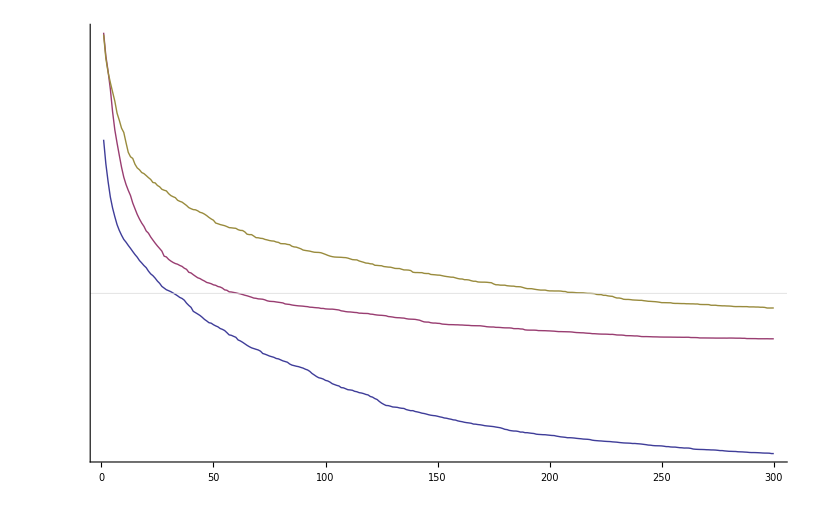

```mathematica
multipleMethods[{"FC_NEAT", "FC_GP", "FC_GPDC"}, "AVG_DISTANCE", 5]
```

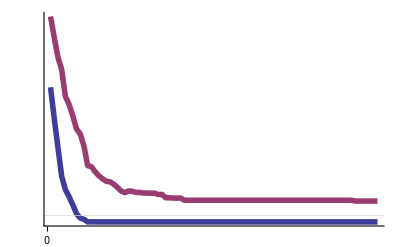

```mathematica
multipleMethods[{"T_NEAT", "T_GP"}, "AVG_DISTANCE", 5]
```

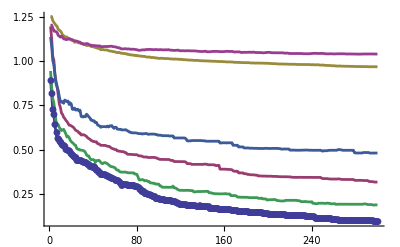

```mathematica
multipleMethods[{"FC_NEAT_7_20", "FC_GP_7_20", "FC_SADE_7_20"}, "AVG_DISTANCE", 5]
```

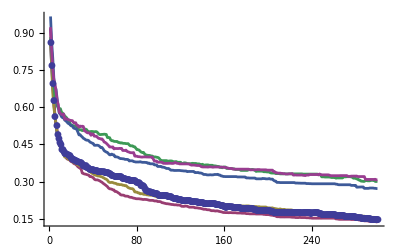

```mathematica
multipleMethods[{"DIV_GP_5_50", "DIV_NEAT_5_50", "DIV_NEAT_5_50_AMP10"}, "AVG_DISTANCE", 5]
```

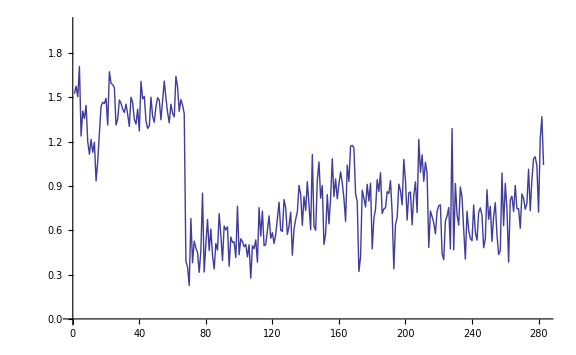

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

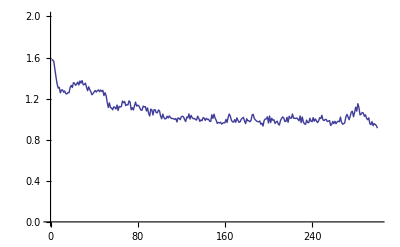

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50"},"DIVERSITY"],PlotRange->{0,2}]
```

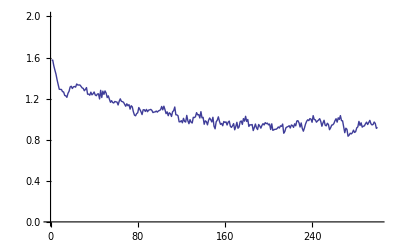

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_5_50_AMP10"},"DIVERSITY"],PlotRange->{0,2}]
```

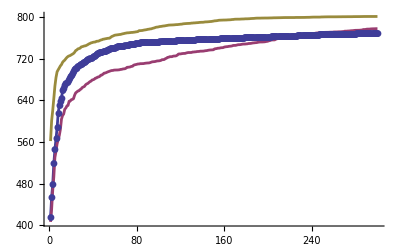

```mathematica
multipleMethods[{"DIV_GP_7_50","DIV_GPC_7_50", "DIV_NEAT_7_50"}, "FITNESS", 2, False]
```

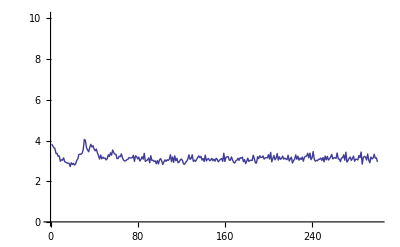

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

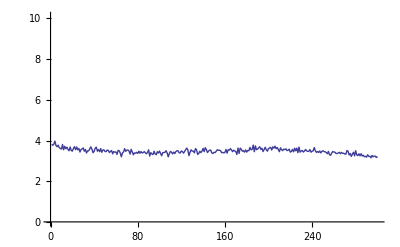

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

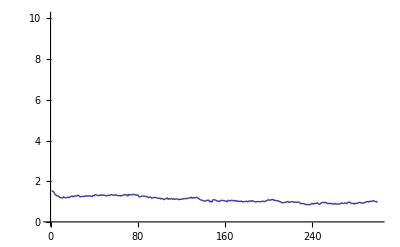

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"P_DIVERSITY"],PlotRange->{0,10.1}]
```

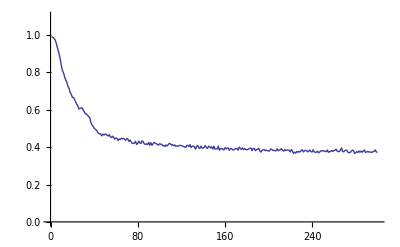

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GP_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

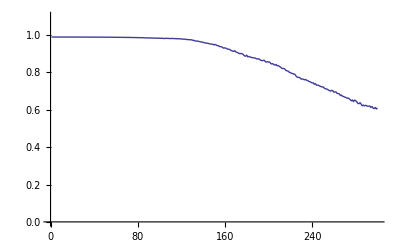

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_GPC_7_50"},"G_DIVERSITY"],PlotRange->{0,1.1}]
```

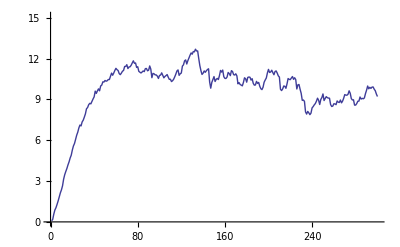

```mathematica
ListLinePlot[singleMethodDiversity[{"DIV_NEAT_7_50"},"G_DIVERSITY"],PlotRange->{0,15.1}]
```

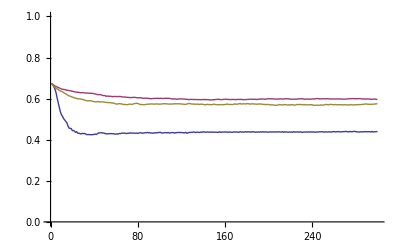

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_ROULETTE"},"G_DIVERSITY"], singleMethodDiversity[{"GEP_TOURNAMENT2"},"G_DIVERSITY"]},PlotRange->{0,1}]
```

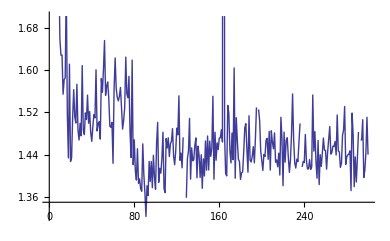

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT"},"P_DIVERSITY"]}]
```

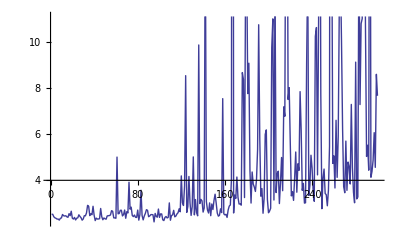

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_TOURNAMENT2"},"P_DIVERSITY"]}]
```

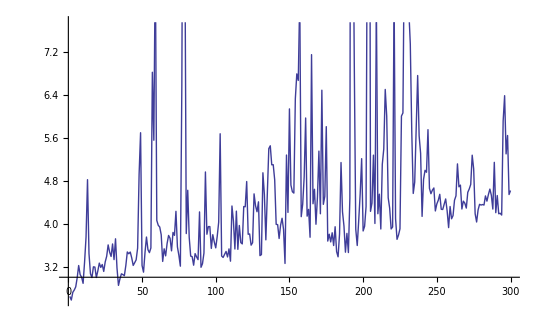

```mathematica
ListLinePlot[{singleMethodDiversity[{"GEP_ROULETTE"},"P_DIVERSITY"]}]
```

## Final Stats

```mathematica
files="~/java/exp/"<>#<>"/experiments_001.txt"&/@{"G0","I0","I1","I2","I3","I4","I5","I6"}
```

{~/java/exp/G0/experiments_001.txt,~/java/exp/I0/experiments_001.txt,~/java/exp/I1/experiments_001.txt,~/java/exp/I2/experiments_001.txt,~/java/exp/I3/experiments_001.txt,~/java/exp/I4/experiments_001.txt,~/java/exp/I5/experiments_001.txt,~/java/exp/I6/experiments_001.txt}

```mathematica
files=listAllExperimentFiles[{"G0","110706123535_1"}]
```

{/Users/drchaj1/java/exp/G0/experiments_001.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_001.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_002.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_003.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_004.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_005.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_006.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_007.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_008.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_009.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_010.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_011.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_012.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_013.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_014.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_015.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_016.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_017.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_018.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_019.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_020.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_021.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_022.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_023.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_024.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_025.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_026.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_027.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_028.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_029.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_030.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_031.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_032.txt,/Users/drchaj1/java/exp/110706123535_1/experiments_033.txt}

```mathematica
files={"~/java/exp/GP/experiments_001.txt","~/java/exp/GPAT/experiments_001.txt"};
```

```mathematica
files={"~/java/exp/I0/experiments_001.txt","~/java/exp/I1/experiments_001.txt","~/java/exp/I2/experiments_001.txt","~/java/exp/I3/experiments_001.txt"};
```

```mathematica
files={"~/java/exp/GP/experiments_001.txt","~/java/exp/GPAT/experiments_001.txt","~/java/exp/GPAT_T/experiments_001.txt","~/java/exp/GPAT_T2/experiments_001.txt"};
```

```mathematica
readFinalStatNames[files]
```

{BSF,BSFG,ARITY_BSF,ARITY_LG,CONSTANTS_BSF,CONSTANTS_LG,DEPTH_BSF,DEPTH_LG,LEAVES_BSF,LEAVES_LG,NODES_BSF,NODES_LG,GENERATIONS,EVALUATIONS,MAX_FITNESS,SUCCESS,TIME}

```mathematica
stats=readFinalStats[files,"BSF"];
```

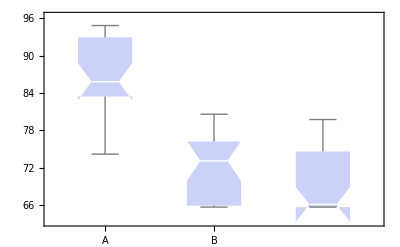

```mathematica
BoxWhiskerChart[stats,"Notched",ChartLabels->{"A","B"}]
```

```mathematica
finalStatsAllBoxPlots[files_,methods_]:=
Module[{statNames},
statNames=readFinalStatNames[files];
Grid[Transpose[{statNames,
BoxWhiskerChart[#,"Notched",ChartLabels->methods,ChartStyle->"Rainbow",ImageSize->800]&
/@(readFinalStats[files,#]&/@statNames)
}]]
]
```

```mathematica
labels={"G0"}~Join~(MapIndexed["S"<>ToString[(Sequence@@#2)]&,Rest[files]])
```

{G0,S1,S2,S3,S4,S5,S6,S7,S8,S9,S10,S11,S12,S13,S14,S15,S16,S17,S18,S19,S20,S21,S22,S23,S24,S25,S26,S27,S28,S29,S30,S31,S32,S33}

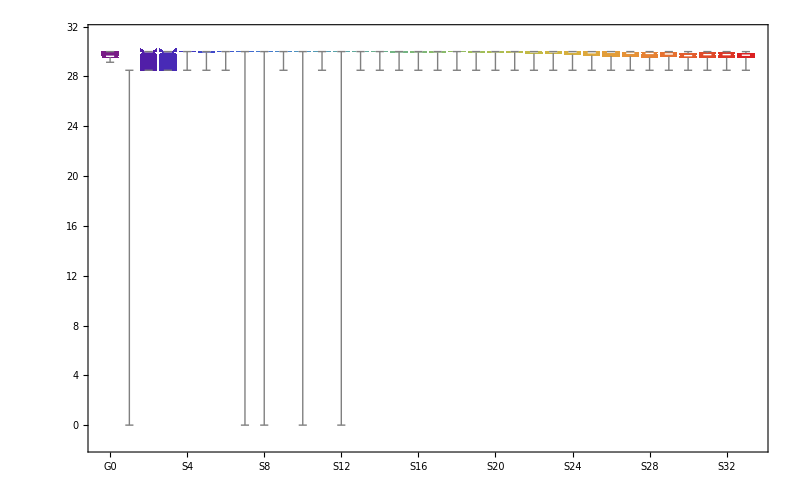
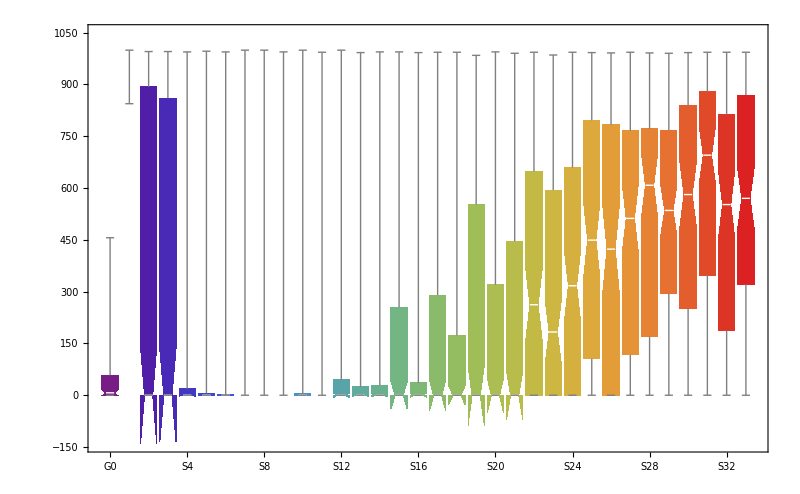
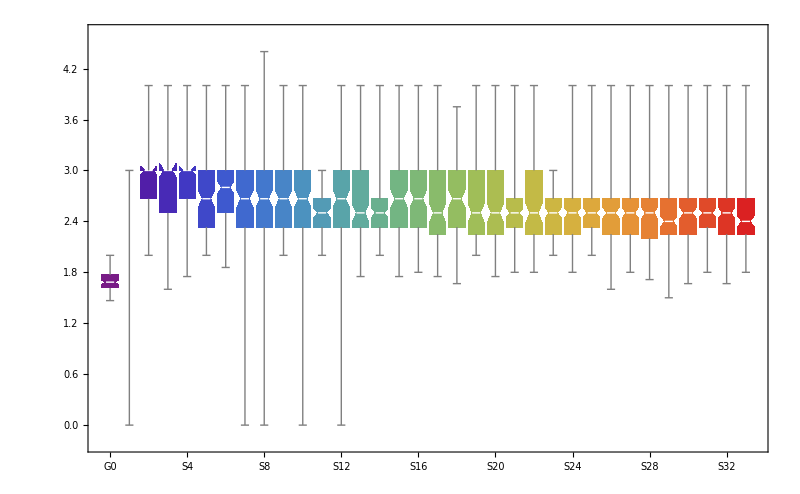
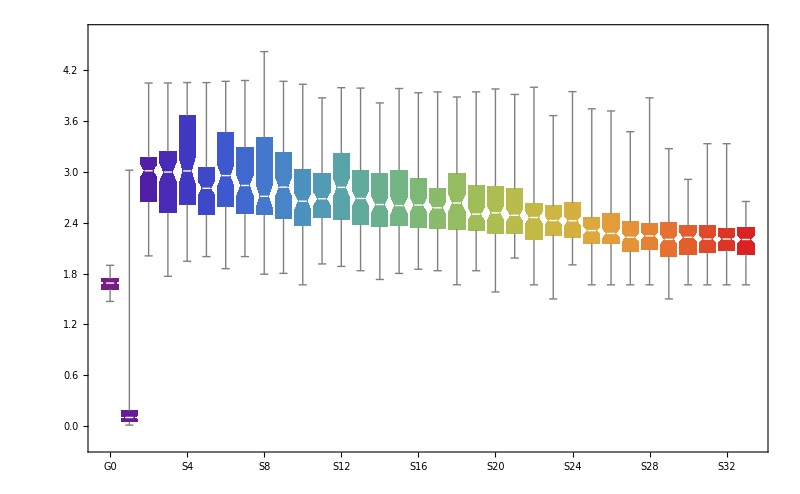
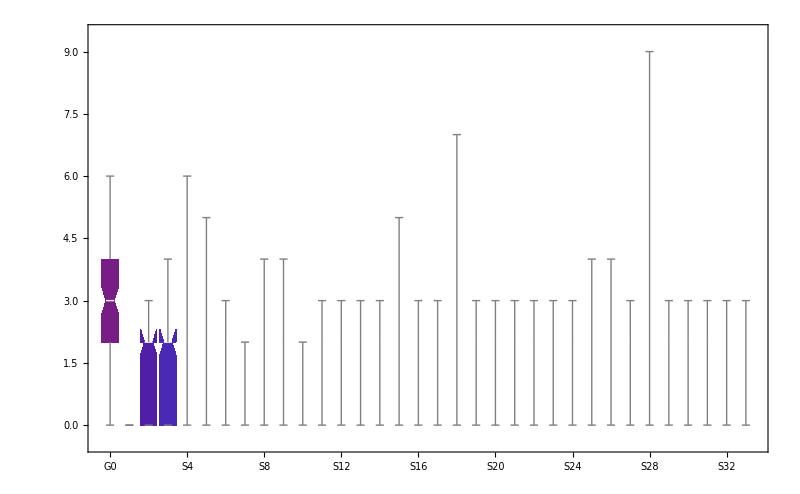
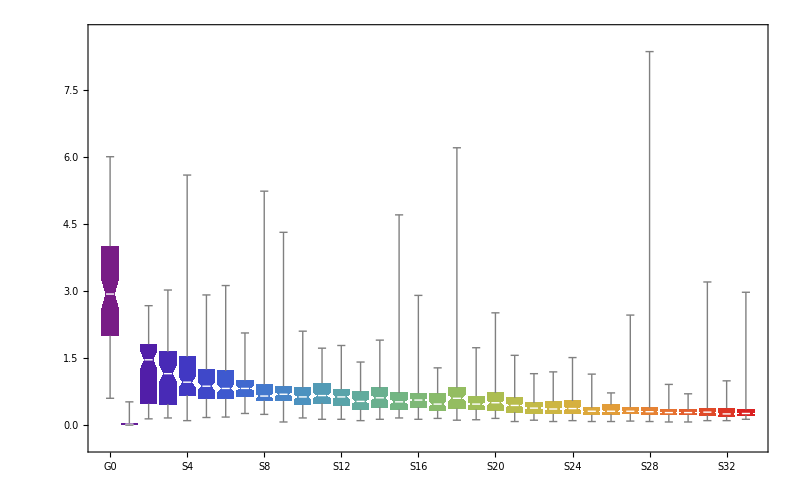
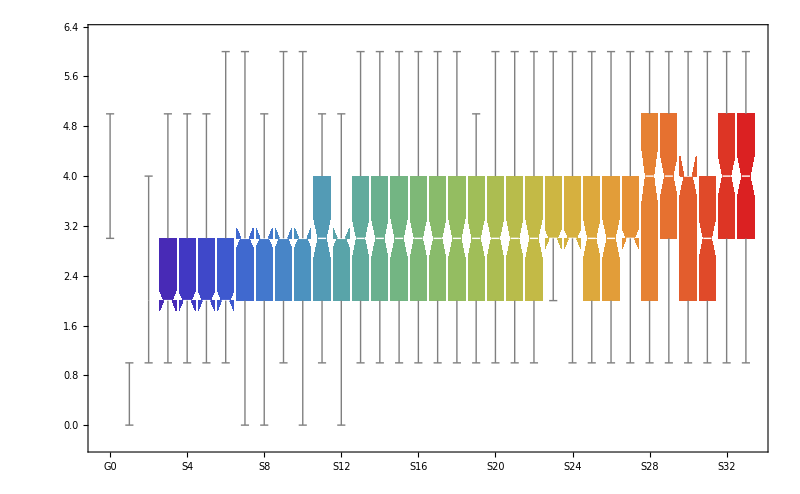
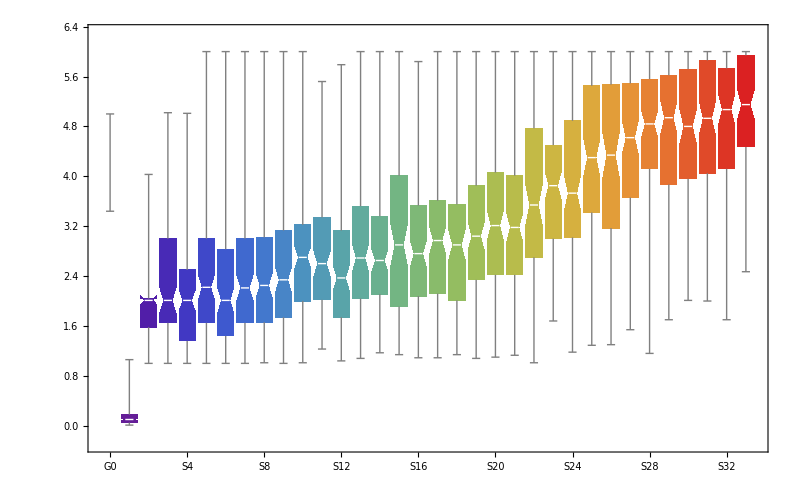
BSF | -Graphics-
BSFG | -Graphics-
ARITY_BSF | -Graphics-
ARITY_LG | -Graphics-
CONSTANTS_BSF | -Graphics-
CONSTANTS_LG | -Graphics-
DEPTH_BSF | -Graphics-
DEPTH_LG | -Graphics-
LEAVES_BSF | -Graphics-
LEAVES_LG | -Graphics-
NODES_BSF | -Graphics-
NODES_LG | -Graphics-
GENERATIONS | -Graphics-
EVALUATIONS | -Graphics-
MAX_FITNESS | -Graphics-
SUCCESS | -Graphics-
TIME | -Graphics-

```mathematica
finalStatsAllBoxPlots[files,labels]
```